```mathematica
res={9925,33968,39343,19790,4373,427,10,0,0,0,0,0,0,33848,108499,121144,57370,12082,1069,23,0,0,0,0,0,0,39439,120329,126959,57005,11572,941,23,0,0,0,0,0,0,19813,57196,57823,24986,4765,394,11,0,0,0,0,0,0,4457,12150,11578,4818,923,69,3,0,0,0,0,0,0,372,1060,936,357,68,4,0,0,0,0,0,0,0,12,23,31,11,1,0,0,0,0,0,0,0,0}
```

{9925,33968,39343,19790,4373,427,10,0,0,0,0,0,0,33848,108499,121144,57370,12082,1069,23,0,0,0,0,0,0,39439,120329,126959,57005,11572,941,23,0,0,0,0,0,0,19813,57196,57823,24986,4765,394,11,0,0,0,0,0,0,4457,12150,11578,4818,923,69,3,0,0,0,0,0,0,372,1060,936,357,68,4,0,0,0,0,0,0,0,12,23,31,11,1,0,0,0,0,0,0,0,0}

```mathematica
norm=Function[#/Plus@@(#)]
```

#1/(Plus@@#1)&

```mathematica
normRes=Map[norm,Partition[res,13]] //N
```

{{0.0920379,0.314997,0.364841,0.183519,0.0405523,0.00395972,0.0000927334,0.,0.,0.,0.,0.,0.},{0.101331,0.324813,0.362669,0.171748,0.0361699,0.00320026,0.0000688551,0.,0.,0.,0.,0.,0.},{0.1107,0.337749,0.356358,0.160006,0.0324812,0.00264127,0.0000645581,0.,0.,0.,0.,0.,0.},{0.120088,0.346668,0.350468,0.151441,0.0288809,0.00238805,0.0000666715,0.,0.,0.,0.,0.,0.},{0.131096,0.357374,0.340549,0.141714,0.0271487,0.00202953,0.0000882405,0.,0.,0.,0.,0.,0.},{0.133,0.378977,0.334644,0.127637,0.0243118,0.0014301,0.,0.,0.,0.,0.,0.,0.},{0.153846,0.294872,0.397436,0.141026,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.}}

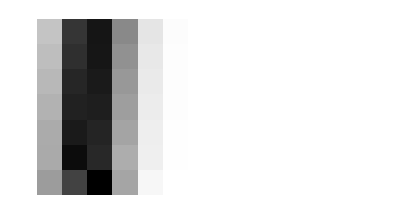

```mathematica
ArrayPlot[normRes]
```

```mathematica
Apply[Plus,Map[#*{0,1,2,3,4,5,6,7,8,9,10,11,12}&,normRes],1]
```

{1.7778,1.72649,1.674,1.62979,1.58289,1.53557,1.5641}

```mathematica
Apply[Plus,Partition[res,13],1]
```

{107836,334035,356268,164988,33998,2797,78}

```mathematica
Apply[Plus,Partition[res,13],{0}]
```

{107866,333225,357814,164337,33784,2904,70,0,0,0,0,0,0}

```mathematica
Partition[res,13]
```

{{9925,33968,39343,19790,4373,427,10,0,0,0,0,0,0},{33848,108499,121144,57370,12082,1069,23,0,0,0,0,0,0},{39439,120329,126959,57005,11572,941,23,0,0,0,0,0,0},{19813,57196,57823,24986,4765,394,11,0,0,0,0,0,0},{4457,12150,11578,4818,923,69,3,0,0,0,0,0,0},{372,1060,936,357,68,4,0,0,0,0,0,0,0},{12,23,31,11,1,0,0,0,0,0,0,0,0}}